```mathematica
Quit[];
```

```mathematica
Li2[z_]:=-π^2/6-1/2 Log[1/-z]^2-PolyLog[2,1/z];
Li3[z_]:=π^2/6 Log[1/-z]+1/6 Log[1/-z]^3+PolyLog[3,1/z];
```

```mathematica
(*Scharf,R.,& Tausk,J.B.(1994).Scalar two-loop integrals for gauge boson self-energy diagrams with a massless fermion loop.Nuclear Physics B,412(3),523-552.*)
(*Looks like the MS-scheme, not MSbar.*)
TwoLoopAmp1[s_,M_]:=-1/s(-Zeta[3]-2Zeta[2](-Log[1/-x]+Log[1/(1-x)])+Log[1/-x]^2 Log[1+x]+2/3 Log[1/(1-x)]^3+(-2Log[1/-x]+4Log[1/(1-x)])Li2[1+x]+4Li3[1+x]+2PolyLog[3,-x]+4Li3[1/(1-x)]+2Li3[x]-4Li3[(1+x)/(1-x)]+4PolyLog[3,(x+1)/(x-1)])/.{x->s/M^2};
TwoLoopAmp2[s_,M_]:=-2(-3/2-1/2(Lp+Lm)^2+Lp+Lm-x/2 Log[-x]+1/2(x-1/x)Log[1-x]+PolyLog[2,x])/.{x->s/M^2,Lp->EulerGamma-Log[(4π)/-s],Lm->EulerGamma-Log[(4π)/M^2]};
```

```mathematica
OneLoopAmp[s_]:=-EulerGamma+2+Log[(4π)/-s];
```

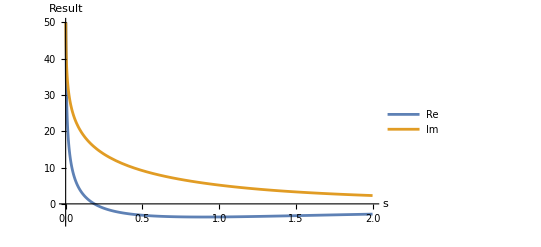

```mathematica
Plot[{Re[TwoLoopAmp1[s,1]],Im[TwoLoopAmp1[s,1]]},{s,0,2},PlotRange->{-5,50},AxesLabel->{s,"Result"},PlotLegends->Placed[{"Re", "Im"}, {Right,Top}]]
```

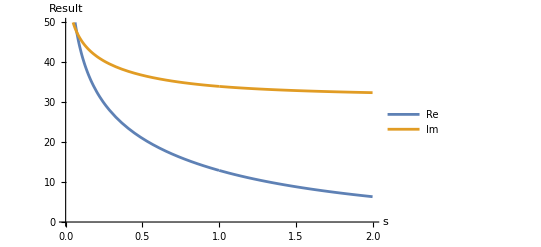

```mathematica
Plot[{Re[TwoLoopAmp2[s,1]],Im[TwoLoopAmp2[s,1]]},{s,0,2},PlotRange->{0,50},AxesLabel->{s,"Result"},PlotLegends->Placed[{"Re", "Im"}, {Right,Top}]]
```

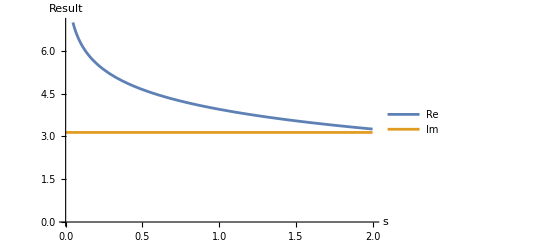

```mathematica
Plot[{Re[OneLoopAmp[s]],Im[OneLoopAmp[s]]},{s,0,2},PlotRange->{0,7},AxesLabel->{s,"Result"},PlotLegends->Placed[{"Re", "Im"}, {Right,Top}]]
```

```mathematica
SelfE[c_,s_,M_]:=c^2(TwoLoopAmp1[s,M]+TwoLoopAmp2[s,M])+c×OneLoopAmp[s];
Propagator2L[c_,s_,M_]:=1/(s-M^2+SelfE[c,s,M]);
Propagator1L[c_,s_,M_]:=1/(s-M^2+c×OneLoopAmp[s]);
```

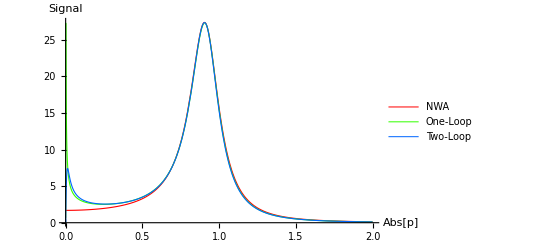

```mathematica
Plot[{1.208 Abs[p^2-0.819+0.21ⅈ]^-2,Abs[Propagator1L[0.0609,p^2,1.036]]^2,Abs[Propagator2L[0.04,p^2,1]]^2},{p,0,2},ImageSize->Full,PlotRange->All,MaxRecursion->15,WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"NWA","One-Loop", "Two-Loop"}, {Right,Top}],AxesLabel->{Sqrt[Abs[p^2]],"Signal"},PlotStyle->Table[Directive[Hue[1+0.3n],Thickness[0.002]],{n,0,2}]]
```

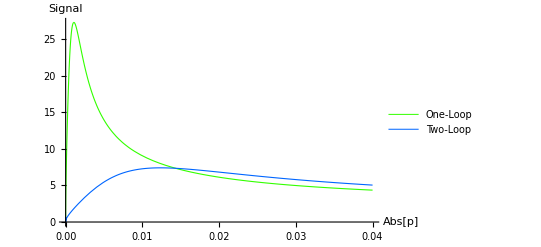

```mathematica
Plot[{Abs[Propagator1L[0.0609,p^2,1.036]]^2,Abs[Propagator2L[0.04,p^2,1]]^2},{p,0,0.04},ImageSize->Full,PlotRange->All,MaxRecursion->15,WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"One-Loop", "Two-Loop"}, {Right,Top}],AxesLabel->{Sqrt[Abs[p^2]],"Signal"},PlotStyle->Table[Directive[Hue[1+0.3n],Thickness[0.002]],{n,1,2}]]
```